```mathematica
(* Run to install FeynCalc 
<<FeynCalc`*)
```

```mathematica
Clear["Global`*"]
```

# Constructing

## Do Wick’s contractions

```mathematica
(* Notation for Matrices in FeynCalc package (in D=4 dimension)

GA[mu] is 
GA[mu, nu] is  (other way is GA[mu].GA[nu])
GA[5] is 
GA[6] is  right projection
GA[7] is  left projection

GS[p] is  (pslash)
*)
```

```mathematica
(* Define vertex of the interaction and propagator for the massless fermion *)
Vertex[ω_,k_,mu_,nu_]:=1/2(-1/4(GA[nu]*(FV[ω,mu]+FV[k,mu]) +GA[mu]*( FV[ω,nu] + FV[k,nu])) -1/2 MT[mu,nu]*(GS[ω]-GS[k]));
Prop[p_]:=I*(GS[p] + M);

(* Rules *)

(* rewrite  et similia *)
Separateql = {
Pair[Momentum[l],Momentum[q*x]]:>Pair[LorentzIndex[α],Momentum[l]]*x*Pair[LorentzIndex[α],Momentum[q]],
Pair[Momentum[x*q],Momentum[l]]:>Pair[LorentzIndex[β],Momentum[l]]*x*Pair[LorentzIndex[β],Momentum[q]],

Pair[Momentum[q],Momentum[l]]:>Pair[LorentzIndex[λ],Momentum[l]]*Pair[LorentzIndex[λ],Momentum[q]],
Pair[Momentum[l],Momentum[q]]:>Pair[LorentzIndex[τ],Momentum[l]]*Pair[LorentzIndex[τ],Momentum[q]]
};

ruleqx = {
(* separate  *)
Pair[LorentzIndex[a_],Momentum[x*q]]:>x*Pair[LorentzIndex[a],Momentum[q]],
Pair[LorentzIndex[a_],Momentum[q*x]]:>x*Pair[LorentzIndex[a],Momentum[q]],

(* separate  *)
Pair[Momentum[x*q],Momentum[x*q]]:>x^2 Pair[Momentum[q],Momentum[q]],
Pair[Momentum[x*q],Momentum[q]]:>x*Pair[Momentum[q],Momentum[q]],
Pair[Momentum[q],Momentum[x*q]]:>x*Pair[Momentum[q],Momentum[q]]
};

ruleqγ = {
DiracGamma[Momentum[q x]]:>x*DiracGamma[Momentum[q]],
DiracGamma[Momentum[x q]]:>x*DiracGamma[Momentum[q]]
};

ruleSeparateLL = {
(* separate  *)
Pair[Momentum[l],Momentum[l]]:> Pair[LorentzIndex[l1],LorentzIndex[l2]]*Pair[LorentzIndex[l1],Momentum[l]]*Pair[LorentzIndex[l2], Momentum[l]]
};

ruleprodLQ = {
(* separate  *)
Pair[Momentum[l],Momentum[q]]:>Pair[LorentzIndex[l3],LorentzIndex[q3]]*Pair[LorentzIndex[l3],Momentum[l]]*Pair[LorentzIndex[q3],Momentum[q]]
};

ruleηlq = {
(* rewrite  *)
Pair[LorentzIndex[a_],LorentzIndex[b_]]^2 Pair[LorentzIndex[a_],Momentum[l]]^2 Pair[LorentzIndex[b_],Momentum[l]]^2:>Pair[LorentzIndex[a],LorentzIndex[b]]* Pair[LorentzIndex[a],Momentum[l]] *Pair[LorentzIndex[b],Momentum[l]]*Pair[LorentzIndex[l4],LorentzIndex[l5]]* Pair[LorentzIndex[l4],Momentum[l]] *Pair[LorentzIndex[l5],Momentum[l]],

(* rewrite  *)
Pair[LorentzIndex[a_],LorentzIndex[b_]]^2 Pair[LorentzIndex[a_],Momentum[l]]^2 Pair[LorentzIndex[b_],Momentum[q]]^2:>Pair[LorentzIndex[a],LorentzIndex[b]]* Pair[LorentzIndex[a],Momentum[l]] *Pair[LorentzIndex[b],Momentum[q]]*Pair[LorentzIndex[l6],LorentzIndex[q6]]* Pair[LorentzIndex[l6],Momentum[l]] *Pair[LorentzIndex[q6],Momentum[q]]
};

ruleωL = {
(* separate  *)
Pair[LorentzIndex[a_],Momentum[ω*l]]:>ω*Pair[LorentzIndex[a],Momentum[l]],
Pair[LorentzIndex[a_],Momentum[l*ω]]:>ω*Pair[LorentzIndex[a],Momentum[l]],

(* separate  *)
Pair[Momentum[ω*l],Momentum[ω*l]]:>ω^2 Pair[Momentum[l],Momentum[l]],
Pair[Momentum[ω*l],Momentum[l]]:>ω*Pair[Momentum[l],Momentum[l]],
Pair[Momentum[l],Momentum[ω*l]]:>ω*Pair[Momentum[l],Momentum[l]]
};
```

```mathematica
(* ω = k-q , k = l + xq -> ω = l + xq - q*)
Vertex1 =Vertex[ l+x*q - q,l+x*q,μ,ν];
Prop1 = Prop[l + x*q - q];
Vertex2 =Vertex[ q-l-x*q,-l-x*q,ρ,σ];
Prop2 = Prop[l+x*q];

(*(-1) factor due to spin statistic *)
NumeratorV= (-1)*Vertex1.Prop1.Vertex2.Prop2 //DiracSimplify;

Numeratornew = ((NumeratorV //. Separateql) //. ruleqx) //.ruleqγ// DiracSimplify;
NumTot = DiracTrace[Numeratornew] //DiracSimplify;

(* Applying rules to rewrite the Numerator *)
NumTotnew = ((NumTot//.ruleSeparateLL)//.ruleprodLQ )//.ruleηlq;

(* Even part *)
NumMinus = NumTotnew /. l->-l;
NumEven = (NumTotnew + NumMinus)/2 // Simplify;

NumFinω = NumEven /. l->ω*l;

(* Expression we work with *)
NumFin = Collect2[2*NumFinω//. ruleωL //Simplify,MT,FV];
```

## Extract terms

```mathematica
(* Extract the costant part *)
zeroTerm = NumFin /. ω->0 // Simplify;

(* Work with the dipendent part *)
NumL = Collect2[(NumFin - zeroTerm // Simplify),MT,FV];

(* check it does not contain costant terms *)
Print["\n (should be zero): ",NumL /. ω->0]

(* Terms with 2  *)
NumLω = NumL/ω^2//Simplify;
ω2Term =Collect2[NumLω/.ω->0//Simplify,MT,FV];

(* Terms with 4  *)
newNumL = NumL - ω^2 * ω2Term //Simplify;
newNumLω = newNumL/ω^4//Simplify;
ω4Term = Collect2[newNumLω/.ω->0 //Simplify,MT,FV];

(* check that we have taken all the terms *)
Print["\n (should be zero): ",NumFin - zeroTerm - ω^2 * ω2Term - ω^4 * ω4Term //Simplify]
```

(should be zero): 0

(should be zero): 0

## Integrate

```mathematica
n = 2;
d = 4 - ϵ;

Δ= x(x-1)SP[q,q]+ M^2;
```

```mathematica
S[mu_,nu_,rho_,sigma_]:=MT[mu,nu]*MT[rho,sigma] + MT[mu,rho]*MT[nu,sigma] + MT[mu,sigma]*MT[nu,rho];

(* substitute  *)
RuleS ={
Pair[LorentzIndex[a_],Momentum[l]]*Pair[LorentzIndex[b_],Momentum[l]]*Pair[LorentzIndex[c_],Momentum[l]]*Pair[LorentzIndex[d_],Momentum[l]]:>S[a,b,c,d]
};
```

```mathematica
I4 = (-1)^n Simplify[Normal[Series[Gamma[n-d/2- 2]/Gamma[n] Δ^(d/2+2-n)/(4π)^(d/2),{ϵ,0,0}]]];
ω4Termnew = Contract[ω4Term]//.ruleSeparateLL;
term4 = Contract[ω4Termnew//.RuleS]//Simplify;
I4term = I4*1/4*term4 //Simplify;
```

```mathematica
(* substitute  *)
Ruleη = {
Pair[LorentzIndex[a_],Momentum[l]]*Pair[LorentzIndex[b_],Momentum[l]]:>Pair[LorentzIndex[a],LorentzIndex[b]]
};
```

```mathematica
I2 = (-1)^(n-1)  Simplify[Normal[Series[Gamma[n-d/2- 1]/Gamma[n] Δ^(d/2+1-n)/(4π)^(d/2),{ϵ,0,0}]]];
term2 = Contract[Collect[ω2Term,l]//.Ruleη]//Simplify;
I2term = I2*1/2*term2;
```

```mathematica
Int[α_] := (-1)^(n+α) Simplify[Normal[Series[(Gamma[n-d/2- α]Gamma[d/2+ α])/(Gamma[n]Gamma[d/2]) Δ^(d/2+α-n)/(4π)^(d/2),{ϵ,0,0}]]];
```

```mathematica
I0term = Int[0]*zeroTerm;
```

```mathematica
(* The result after integration in  *)
FinalResult =( I4term + I0term + I2term )/.SP[q,q]->Pair[Momentum[q],Momentum[q]]// Simplify;
```

## Take imaginary part

```mathematica
subLog = FinalResult/. Log[M^2+(-1+x) x Pair[Momentum[q],Momentum[q]]]->Log[z] // Simplify;
divLog = subLog/Log[z] // Simplify;
limLog = Limit[Limit[divLog,{z->∞}],{ϵ->0}];
resfin = π*limLog;

x1 = 1/2-1/2 √((-4 M^2+Pair[Momentum[q],Momentum[q]])/Pair[Momentum[q],Momentum[q]]) ;
x2 = 1/2+1/2 √((-4 M^2+Pair[Momentum[q],Momentum[q]])/Pair[Momentum[q],Momentum[q]]); 
ΠTensor = Integrate[resfin,{x,x1,x2}]//Simplify;
Print["\n Π = ",Collect2[ΠTensor,FV,MT]]
```

Π = -1/(1920 π (q̄)^4)((q̄)^2-4 M^2) √(((q̄)^2-4 M^2)/(q̄)^2) (3 (ḡ)^μσ (ḡ)^νρ (q̄)^6+3 (ḡ)^μρ (ḡ)^νσ (q̄)^6-2 (ḡ)^μν (ḡ)^ρσ (q̄)^6+8 M^2 (ḡ)^μσ (ḡ)^νρ (q̄)^4+8 M^2 (ḡ)^μρ (ḡ)^νσ (q̄)^4+8 M^2 (ḡ)^μν (ḡ)^ρσ (q̄)^4+2 (q̄)^μ (q̄)^ν (ḡ)^ρσ (q̄)^4-3 (q̄)^μ (ḡ)^νσ (q̄)^ρ (q̄)^4-3 (ḡ)^μσ (q̄)^ν (q̄)^ρ (q̄)^4-3 (q̄)^μ (ḡ)^νρ (q̄)^σ (q̄)^4-3 (ḡ)^μρ (q̄)^ν (q̄)^σ (q̄)^4+2 (ḡ)^μν (q̄)^ρ (q̄)^σ (q̄)^4-8 M^2 (q̄)^μ (q̄)^ν (ḡ)^ρσ (q̄)^2-8 M^2 (q̄)^μ (ḡ)^νσ (q̄)^ρ (q̄)^2-8 M^2 (ḡ)^μσ (q̄)^ν (q̄)^ρ (q̄)^2-8 M^2 (q̄)^μ (ḡ)^νρ (q̄)^σ (q̄)^2-8 M^2 (ḡ)^μρ (q̄)^ν (q̄)^σ (q̄)^2-8 M^2 (ḡ)^μν (q̄)^ρ (q̄)^σ (q̄)^2+4 (q̄)^μ (q̄)^ν (q̄)^ρ (q̄)^σ (q̄)^2+24 M^2 (q̄)^μ (q̄)^ν (q̄)^ρ (q̄)^σ)

## Check for the result in massless case

```mathematica
πtens[mu_,nu_]:=Pair[LorentzIndex[mu],Momentum[q]]*Pair[LorentzIndex[nu],Momentum[q]]- Pair[LorentzIndex[mu],LorentzIndex[nu]]*Pair[Momentum[q],Momentum[q]] ;

Πtens = 2*πtens[μ,ν]*πtens[ρ,σ] - 3*πtens[μ,ρ]*πtens[ν,σ] - 3*πtens[μ,σ]*πtens[ν,ρ];

ResultΠ = 4/(7680 π^2)Πtens*π;
Print["\n (should be zero): ",Collect2[((ΠTensor - ResultΠ)/.M->0)//Simplify,MT,FV]]
```

(should be zero): 0

## Real and Imaginary part of the Tensor

```mathematica
serieResult = Series[FinalResult,{ϵ,0,0}];

(* consider the  part of FinalResult *)
NoPolesPart = SeriesCoefficient[serieResult,0];

(*
(* Integrate to extract both the Real and Imaginary part *)
TensorFinal = Integrate[NoPolesPart,{x,0,1}];

(* Assume  *)
Πtensor = Simplify[TensorFinal,Assumptions->SP[q,q]<0];

subX = Πtensor/.Log[SP[q,q]]->X //Simplify;
(* when  has  the imaginary part is  *)
Imtens = subX/. X->-ⅈ*π //Simplify;

(* Look at the expression and extract by hand the imaginary part, which we define in the next step
Imtensnew = Collect[Imtens,π] //StandardForm;
*)*)
```

# Towards the abundance estimation

## Tensorial perturbation

```mathematica
(* spatial metric and vector *)
η3D=-IdentityMatrix[3];
q3D={qx,qy,qz};

(* Rule to pass from FeynCalc expression to Table *)
Rule3DFeynToTable={
Pair[LorentzIndex[a_],LorentzIndex[b_]]:>η3D[[a,b]],

Pair[LorentzIndex[a_],Momentum[q]]:>q3D[[a]],
Pair[ExplicitLorentzIndex[a_],Momentum[q]]:>q3D[[a]],

Pair[Momentum[q],Momentum[q]]:>q0^2 - Sum[q3D[[i]]^2,{i,1,3}]
};

Rulefinal ={
qx^2+qy^2+qz^2:>Q^2,
-qx^2-qy^2-qz^2:>-Q^2,
(qx^2+qy^2+qz^2)^2:>Q^4,
(-qx^2-qy^2-qz^2)^2:>Q^4
 };
```

## Transverse, Traceless Projectors (and symmetric in and ) in 2D in 4D

```mathematica
(* Define the transverse traceless projector *)
qdir = q3D/Sqrt[Sum[q3D[[i]]^2 , {i,1,3}]];

PTT2D=Table[KroneckerDelta[i,j]-qdir[[i]]*qdir[[j]],{i,1,3},{j,1,3}];

PTT4D=Table[1/2(PTT2D[[i,k]]*PTT2D[[j,r]]+PTT2D[[i,r]]*PTT2D[[j,k]])-1/2 PTT2D[[i,j]]*PTT2D[[k,r]],{i,1,3},{j,1,3},{k,1,3},{r,1,3}];
```

## Define with tables

```mathematica
(* Map the result IMTensor and IMTensorMassive to a table, so easier to manage with indices and contractions *)

(* the Table has 3x3x3x3 dimension *)
TTtable3D=(Table[ΠTensor,{μ,1,3},{ν,1,3},{ρ,1,3},{σ,1,3}] //. Rule3DFeynToTable)//Simplify;
```

```mathematica
(* Projecting and summing over indices*)
fh=-(Sum[PTT4D[[i,j,k,r]]*TTtable3D[[i,j,k,r]],{i,1,3},{j,1,3},{k,1,3},{r,1,3}]//Simplify )//.Rulefinal //Simplify;

(* check of the known result in the massless limit*)
Print["\n (should be zero): ",((8π*fh -((q0^2 - Q^2)^2)/20)/.M->0)//Simplify]
```

(should be zero): 0

## Scalar perturbation

```mathematica
η4D = {{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}};
q4D = {q0,qx,qy,qz};

q4Dlower = η4D.q4D;

(* Rule in 4D to pass from FeynCalc expression to Table *)
Rule4DFeynToTable={
Pair[LorentzIndex[a_],LorentzIndex[b_]]:>η4D[[a,b]],
Pair[ExplicitLorentzIndex[a_],ExplicitLorentzIndex[b_]]:>η4D[[a,b]],

Pair[LorentzIndex[a_],Momentum[q]]:>q4D[[a]],
Pair[ExplicitLorentzIndex[a_],Momentum[q]]:>q4D[[a]],

Pair[Momentum[q],Momentum[q]]:>q0^2 - Sum[q3D[[i]]^2,{i,1,3}]
};
```

## Define with tables

```mathematica
(* Map the result IMTensor and IMTensorMassive to a table, so easier to manage with indices and contractions *)

(* the Table has 4x4x4x4 dimension *)
TTtable4D=(Table[ΠTensor,{μ,1,4},{ν,1,4},{ρ,1,4},{σ,1,4}] //. Rule4DFeynToTable) //Simplify;
```

```mathematica
fΘ=(-Sum[TTtable3D[[μ,μ,ρ,ρ]],{μ,1,3},{ρ,1,3}]//Simplify)//.Rulefinal //Simplify;

(* check if we get what known in the massless limit *)
Print["\n (should be zero): ",(Q^4/30-fΘ*2*8π/.M->0)//Simplify]
```

(should be zero): 0

## Scalar perturbation

```mathematica
(* Contracting with metric tensor (here is simpler using the FeynCalc expression)*)
fΣ=((-Contract[MT[μ,ν]*MT[ρ,σ]*ΠTensor]//Simplify)//.Rule4DFeynToTable)//.Rulefinal//Simplify;

(* check if we get what known in the massless limit *)
Print["\n (should be zero): ",fΣ/.M->0]
```

(should be zero): 0

## Vectorial perturbation

```mathematica
W3D = {Wx,Wy,Wz};
WT = Table[Sum[PTT2D[[i,j]]*W3D[[j]],{j,1,3}],{i,1,3}];

(* momentum space  *)
WTable = I*Table[q3D[[i]]*WT[[j]] + q3D[[j]]*WT[[i]],{i,1,3},{j,1,3}]//Simplify;

(* check of trasversality *)
Print["\n (should be zero): ",WT.q3D//Simplify]
```

(should be zero): 0

```mathematica
(* Contracting *)
fW=Sum[WTable[[i,j]]*WTable[[k,r]]*TTtable3D[[i,j,k,r]],{i,1,3},{j,1,3},{k,1,3},{r,1,3}] //Simplify
```

-1/(480 π (-q0^2+qx^2+qy^2+qz^2))q0^2 (8 M^2+3 q0^2-3 qx^2-3 qy^2-3 qz^2) (-4 M^2+q0^2-qx^2-qy^2-qz^2) √((4 M^2-q0^2+qx^2+qy^2+qz^2)/(-q0^2+qx^2+qy^2+qz^2)) (qx^2 (Wy^2+Wz^2)-2 qy Wy (qx Wx+qz Wz)-2 qx qz Wx Wz+qy^2 (Wx^2+Wz^2)+qz^2 (Wx^2+Wy^2))

```mathematica
(* Look that the term could be rewritten as  and from the trasversality of ,
that's simply *)
```

```mathematica
fWnew = (((fW/. {(qz^2 (Wx^2+Wy^2)-2 qx qz Wx Wz-2 qy Wy (qx Wx+qz Wz)+qy^2 (Wx^2+Wz^2)+qx^2 (Wy^2+Wz^2))->Sum[q3D[[i]]^2,{i,1,3}]}//Simplify)//.Rulefinal )/.-3 qx^2-3 qy^2-3 qz^2->-3 Q^2)//Simplify;

(* check of the known result *)
Print["\n (should be zero): ",(((8π*fWnew-(q0^2 Q^2(q0^2 - Q^2))/20)/.M->0)//.Rulefinal)//Simplify]
```

(should be zero): 0

## Kernels and Plots

```mathematica
(* Kernels *)
funzh[q0_,Q_,M_]=8π*fh;
funzW[q0_,Q_,M_]=8π*fWnew;
funzΣ[q0_,Q_,M_]=8π*fΣ;
funzΘ[q0_,Q_,M_]=8π*fΘ;

Print["\n fΘ = ",funzΘ[q0,q,M]]
Print["\n fΣ = ",funzΣ[q0,q,M]]
Print["\n fW = ",funzW[q0,q,M]]
Print["\n fh = ",funzh[q0,q,M]]

(* Adimensional kernels  , *)
Funzhnew[x_,y_]:=funzh[q0,q,M]/.{M->x,q->y,q0->1};
FunzWnew[x_,y_]:=funzW[q0,q,M]/q^2/.{M->x,q->y,q0->1};
FunzΣnew[x_,y_]:=funzΣ[q0,q,M]/.{M->x,q->y,q0->1};
FunzΘnew[x_,y_]:=funzΘ[q0,q,M]/.{M->x,q->y,q0->1};

(* Check dimensionality *)
Print["\n (should be zero): ",Funzhnew[M/q0,q/q0]*q0^4 - funzh[q0,q,M]//Simplify]
Print["\n (should be zero): ",FunzWnew[M/q0,q/q0]*q0^4 q^2 - funzW[q0,q,M]//Simplify]
Print["\n (should be zero): ",FunzΣnew[M/q0,q/q0]*q0^4 - funzΣ[q0,q,M]//Simplify]
Print["\n (should be zero): ",FunzΘnew[M/q0,q/q0]*q0^4 - funzΘ[q0,q,M]//Simplify]
```

fΘ = ((4 M^2+q^2-q0^2) √((4 M^2)/(q^2-q0^2)+1) (q^6-q0^2 q^4-2 M^2 (8 q^4-20 q0^2 q^2+15 q0^4)))/(60 (q^2-q0^2)^2)

fΣ = -1/2 M^2 (4 M^2+q^2-q0^2) √((4 M^2)/(q^2-q0^2)+1)

fW = -1/60 q^2 q0^2 (-8 M^2+3 q^2-3 q0^2) ((4 M^2+q^2-q0^2)/(q^2-q0^2))^(3/2)

fh = 1/60 (-8 M^2+3 q^2-3 q0^2) (4 M^2+q^2-q0^2) √((4 M^2)/(q^2-q0^2)+1)

(should be zero): 0

(should be zero): 0

(should be zero): 0

«1 more identical outputs»

```mathematica
(* From the Kernel factor  
From the condition *)
Reduce[(4x^2)/(y^2 - 1)+1>=0&&1-y^2>=4x^2&&x>0&&y>0,y]
```

0<x<1/2∧0<y≤√(1-4 x^2)

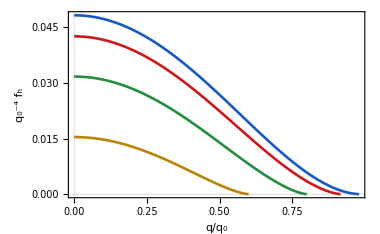

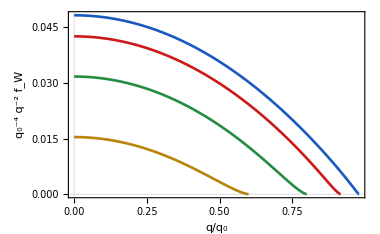

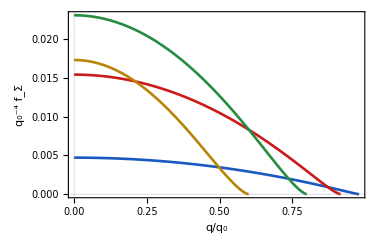

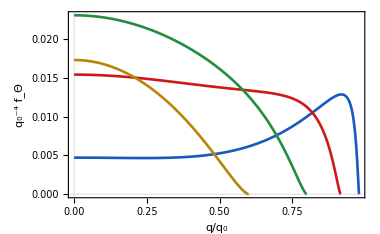

M / q_0

```mathematica
xvalues=Range[0.1,0.4,0.1]; (* 0< x <1/2*)

thesisColors={RGBColor[0.10,0.35,0.75],(*Blu Classico*)
RGBColor[0.80,0.10,0.10],(*Rosso*)
RGBColor[0.15,0.55,0.25],(*Verde Foresta*)
RGBColor[0.72,0.52,0.04],(*Giallo Scuro/Oro*)
RGBColor[0.45,0.15,0.55]  (*Viola/Indaco per il 5° valore*)
};

scientificPlotOptions[yLabel_]:=Sequence[PlotTheme->"Scientific",Frame->True,PlotStyle->Table[Directive[Thickness[0.005],thesisColors[[i]]],{i,Length[xvalues]}],FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[DisplayForm[FormBox[RowBox[{Style["q",Italic],"/",Subscript[Style["q",Italic],"0"]}],TraditionalForm]],FontSize->16],Style[DisplayForm[FormBox[RowBox[{Superscript[Subscript[Style["q",Italic],Style["0",Italic]],Style["-4",Italic]],yLabel}],TraditionalForm]],FontSize->16]},PlotLabel->None,PlotLegends->None,BaseStyle->{FontFamily->"Times",FontSize->11},ImageSize->380,PlotRange->All,MaxRecursion->6,Exclusions->None];

scientificPlotOptions2[yLabel_]:=Sequence[PlotTheme->"Scientific",Frame->True,PlotStyle->Table[Directive[Thickness[0.005],thesisColors[[i]]],{i,Length[xvalues]}],FrameStyle->Directive[Black,AbsoluteThickness[1.2]],FrameTicksStyle->Directive[Black,FontFamily->"Times",FontSize->14],FrameLabel->{Style[DisplayForm[FormBox[RowBox[{Style["q",Italic],"/",Subscript[Style["q",Italic],"0"]}],TraditionalForm]],FontSize->16],Style[DisplayForm[FormBox[RowBox[{Superscript[Subscript[Style["q",Italic],Style["0",Italic]],Style["-4",Italic]],Superscript[Style["q",Italic],Style["-2",Italic]],yLabel}],TraditionalForm]],FontSize->16]},PlotLabel->None,PlotLegends->None,BaseStyle->{FontFamily->"Times",FontSize->11},ImageSize->380,PlotRange->All,MaxRecursion->6,Exclusions->None];

 plotTensor=Plot[Evaluate[Table[ConditionalExpression[Funzhnew[x,y],y<=Sqrt[1-4x^2]],{x,xvalues}]],{y,10^-5,1},Evaluate@scientificPlotOptions[Subscript[Style["f",Italic],Style["h",Italic]]]];Print[plotTensor];

plotVector=Plot[Evaluate[Table[ConditionalExpression[FunzWnew[x,y],y<=Sqrt[1-4x^2]],{x,xvalues}]],{y,10^-5,1},Evaluate@scientificPlotOptions2[Subscript[Style["f",Italic],Style["W",Italic]]]];Print[plotVector];

plotSigma=Plot[Evaluate[Table[ConditionalExpression[FunzΣnew[x,y],y<=Sqrt[1-4x^2]],{x,xvalues}]],{y,10^-5,1},Evaluate@scientificPlotOptions[Subscript[Style["f",Italic],Style["Σ",Italic]]]];Print[plotSigma];

 plotTheta=Plot[Evaluate[Table[ConditionalExpression[FunzΘnew[x,y],y<=Sqrt[1-4x^2]],{x,xvalues}]],{y,10^-5,1},Evaluate@scientificPlotOptions[Subscript[Style["f",Italic],Style["Θ",Italic]]]];Print[plotTheta]

legendStandaloneBox=Framed[Column[{Style[Row[{Style["M",Italic]," / ",Subscript[Style["q",Italic],"0"]}],12,Bold,FontFamily->"Times New Roman"],Spacer[6],LineLegend[thesisColors,Table[NumberForm[x,{2,3}],{x,xvalues}],LabelStyle->{FontFamily->"Times New Roman",FontSize->11,GrayLevel[0.15]},Spacings->{0.5,0.6},LegendMarkerSize->{20,3.5},LegendLayout->"Vertical"]},Alignment->Center],FrameStyle->Directive[GrayLevel[0.72],Thickness[0.0015]],Background->GrayLevel[0.98],RoundingRadius->4,FrameMargins->{{10,10},{8,10}} ];
```